# Figures for Reaching for Yield

## Numerical Solutions for Geometric Average Model

```mathematica
ColorList=ColorData[97,"ColorList"];
Col1=ColorList[[1]];
Col2=ColorList[[2]];
Col3=ColorList[[3]];
Clear[f,μ,σ];
f=(rf+α μ-1/2 α^2 σ^2)/(1-γ)-1/2 α(μ-α σ^2)+(ρ(μ-α σ^2))/((1-γ)^2 α σ^2);
rfList=Range[-0.2,0.07,0.0005];
Consumption=rf+α μ-1/2 α^2 σ^2;
toSolve={f==0&&α>0&&Consumption>0&&μ-α σ^2>0};
A=-(rf+α μ-1/2 α^2 σ^2)^-γ(μ-α σ^2)/((1-γ)α σ^2);
rfCompStat=-γ(rf+α μ-1/2 α^2 σ^2)^(-γ-1)(μ-α σ^2)+(1-γ)D[A,rf]α σ^2;
```

Comparing Portfolio Allocation for different values of risk premium

```mathematica
ListPlot[{
Table[{rf,α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.05,σ->0.18},α,Reals]][[1]]},{rf,rfList}],	
Table[{rf,α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.06,σ->0.18},α,Reals]][[1]]},{rf,rfList}],
Table[{rf,α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.07,σ->0.18},α,Reals]][[1]]},{rf,rfList}]},
PlotLabels->{"μ=0.05","μ=0.06","μ=0.07"},AxesLabel->{"r_f","Risky Share α"},
PlotRange->{0.2,1.15},Joined->True,BaseStyle->{FontSize->12}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Figure with investment under one-sided constraint

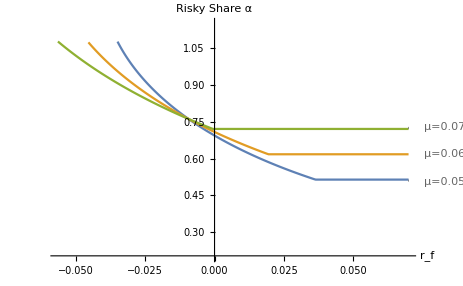

```mathematica
ListPlot[{
Table[{rf,Max[α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.05,σ->0.18},α,Reals]][[1]],μ/(γ σ^2)/.{γ->3,ρ->0.075,μ->0.05,σ->0.18}]},{rf,rfList}],	
Table[{rf,Max[α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.06,σ->0.18},α,Reals]][[1]],μ/(γ σ^2)/.{γ->3,ρ->0.075,μ->0.06,σ->0.18}]},{rf,rfList}],
Table[{rf,Max[α/.Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.07,σ->0.18},α,Reals]][[1]],μ/(γ σ^2)/.{γ->3,ρ->0.075,μ->0.07,σ->0.18}]},{rf,rfList}]},
PlotLabels->{"μ=0.05","μ=0.06","μ=0.07"},AxesLabel->{"r_f","Risky Share α"},
PlotRange->{0.2,1.15},Joined->True,BaseStyle->{FontSize->12}]
```

Plotting Average Return portfolio return for a constrained agent

```mathematica
rfList=Range[-0.06,0.10,0.0005];
BaseParams={ρ->0.075,μ->0.06,σ->0.18};
p1=ListPlot[{
Table[{rf,(rf+α μ)/.Evaluate[NSolve[toSolve/.{γ->2}/.BaseParams,α,Reals]][[1]]/.{γ->2}/.BaseParams},{rf,rfList}],
Table[{rf,(rf+α μ)/.Evaluate[NSolve[toSolve/.{γ->3}/.BaseParams,α,Reals]][[1]]/.{γ->3}/.BaseParams},{rf,rfList}],
Table[{rf,rf},{rf,rfList}],
Table[{rf,(rf+μ^2/σ^2 )/.BaseParams},{rf,rfList}]
},AxesLabel->{"r_f","Average Return r_f+αμ"},
PlotLabels->{"γ=2","γ=3"},
Joined->True, BaseStyle->{FontSize->12},
PlotStyle->Join[ColorData[97,"ColorList"][[1;;2]],{Black,Black}]
]
```

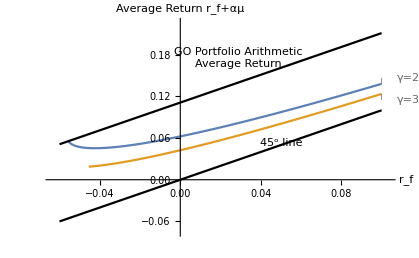

Plotting consumption-to-wealth ratio and comparing with that of the standard model

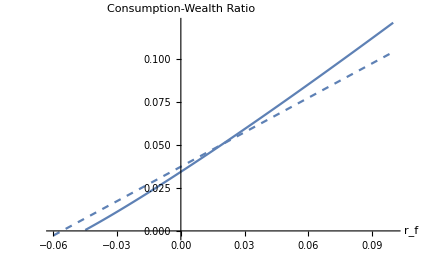

```mathematica
rfList=Range[-0.06,0.10,0.001];
BaseParams={ρ->0.075,μ->0.06,σ->0.18};
p1=ListPlot[{
Table[{rf,(rf+α μ-1/2 α^2 σ^2)/.Evaluate[NSolve[toSolve/.{γ->3}/.BaseParams,α,Reals]][[1]]/.{γ->3}/.BaseParams},{rf,rfList}],
Table[{rf,(ρ/γ+(γ-1)/γ(rf+1/(2γ)(μ/σ)^2 ))/.{γ->3}/.BaseParams},{rf,rfList}]
},AxesLabel->{"r_f","Consumption-Wealth Ratio"},
Joined->True, BaseStyle->{FontSize->12},
PlotStyle->{{Col1},{Col1,Dashed}}
]
```

```mathematica
(ρ/γ+(γ-1)/γ(rf+1/(2γ)(μ/σ)^2 ))/.BaseParams
```

0.075/γ+((rf+0.0555556/γ) (-1+γ))/γ

## Mean-Standard-Deviation Diagrams

Comparing Arithmetic and Geometric Average Model

```mathematica
ClearAll[v];
c0utility=(ρ-(1-γ)^2 σc^2/2)^(-1/(γ-1))(1/((1-γ)v))^(1/(γ-1));
c0port=rf+σc/σ μ-1/2 σc^2;
c0utilityAR=(ρ-γ(γ-1) σc^2/2)^(-1/(γ-1))(1/((1-γ)v))^(1/(γ-1));
c0portAR=rf+σc/σ μ;
baseparams = {rf->0.02,μ->0.06,σ->0.18,γ-> 3,ρ->0.075,v->-3750};
AsymptoteGeom=Max[σc/.Solve[ρ-(1-γ)^2 σc^2/2==0,σc]/.baseparams];
AsymptoteAr=Max[σc/.Solve[ρ-γ(γ-1) σc^2/2==0,σc]/.baseparams];
LineAsymptoteGeom=Line[{{AsymptoteGeom,-100},{AsymptoteGeom,100}}];
LineAsymptoteAr=Line[{{AsymptoteAr,-100},{AsymptoteAr,100}}];
ColorList=ColorData[97,"ColorList"];
GreenCol=RGBColor[68/256,168/256,68/256,1]; (* Picking a good green color*)
Plot[{c0utilityAR/.baseparams,
				c0portAR/.baseparams,
				c0utility/.baseparams, 
				c0port/.baseparams},{σc,0,0.2},
	PlotRange->{0.01,0.13},
	PlotStyle->{ColorList[[1]],{ColorList[[1]], Dashed},ColorList[[2]],{ColorList[[2]], Dashed}},
	AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12},
Epilog->{{Directive[{ColorList[[1]],Thickness[0.005]}],LineAsymptoteAr},{Directive[{ColorList[[2]],Thickness[0.005]}],LineAsymptoteGeom}}]
```

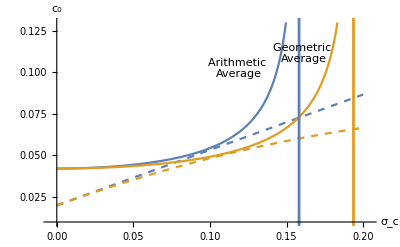

### Comparative Statics on Mean-Standard Deviation Diagrams

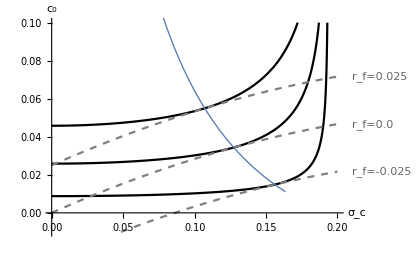

/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/graph_analysis_vary_rf.pdf

```mathematica
ClearAll[c01,c02];
c01=(ρ-(1-γ)^2 σc^2/2)^(-1/(γ-1))(1/((1-γ)v))^(1/(γ-1));
c02=rf+σc/σ μ-1/2 σc^2;
params1={rf->-0.025,μ->0.06,σ->0.18,γ-> 3,ρ->0.075,Infl->0};
params2={rf->0.0,μ->0.06,σ->0.18,γ-> 3,ρ->0.075,Infl->0};
params3={rf->0.025,μ->0.06,σ->0.18,γ-> 3,ρ->0.075,Infl->0};
baseparams={μ->0.06,σ->0.18,γ-> 3,ρ->0.075,Infl->0};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
vsol1=v/.sol1;
vsol2=v/.sol2;
vsol3=v/.sol3;
rfList=Range[-0.03,0.5,0.002];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]]/.baseparams},{rfsub,rfList}];
p1=Plot[{c01/.params1/.{v->vsol1},c02/.params1/.{v->vsol1},
	c01/.params2/.{v->vsol2},c02/.params2/.{v->vsol2},
	c01/.params3/.{v->vsol3},c02/.params3/.{v->vsol3}},
{σc,0,0.2},PlotRange->{-0.01,0.1},PlotStyle->{Black,{Dashed,Gray}},
PlotLabels->{None,"r_f=-0.025",None,"r_f=0.0",None,"r_f=0.025"},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->Thick, Joined->True,PlotStyle->PointSize[0.05]];
figure2=Show[p1,p2]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/graph_analysis_vary_rf.pdf",figure2,"PDF"]
```

```mathematica
params1={rf->0.02,μ->0.06,σ->0.18,γ-> 3,ρ->0.05};
params2={rf->0.02,μ->0.06,σ->0.18,γ-> 3,ρ->0.075};
params3={rf->0.02,μ->0.06,σ->0.18,γ-> 3,ρ->0.10};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
ρList=Range[0.01,0.2,0.005];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0};
baseparams={μ->0.06,σ->0.18,γ-> 3,rf->0.02};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{ρ->ρsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{ρ->ρsub},{σc,v},Reals][[1]]/.baseparams/.{ρ->ρsub}},{ρsub,{0.05,0.075,0.10}}];
p1=Plot[{c01/.params1/.sol1,c02/.params1/.sol1,
	c01/.params2/.sol2,c02/.params2/.sol2,
	c01/.params3/.sol3,c02/.params3/.sol3},
{σc,0.05,0.16},PlotRange->{0.03,0.06},PlotStyle->{Black,{Dashed,Gray}},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->PointSize[0.02]];
Show[p1,p2]
```

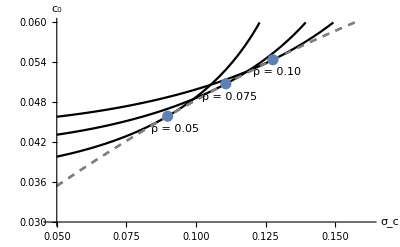

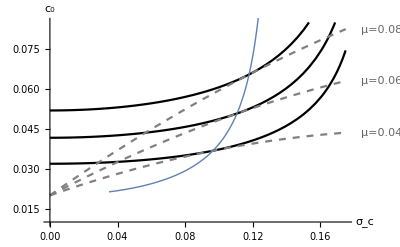

```mathematica
params1={rf->0.02,μ->0.04,σ->0.18,γ-> 3,ρ->0.075};
params2={rf->0.02,μ->0.06,σ->0.18,γ-> 3,ρ->0.075};
params3={rf->0.02,μ->0.08,σ->0.18,γ-> 3,ρ->0.075};
baseparams={rf->0.02,σ->0.18,γ-> 3,ρ->0.075};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
μList=Range[0.01,0.12,0.001];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{μ->μsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{μ->μsub},{σc,v},Reals][[1]]/.baseparams/.{μ->μsub}},{μsub,μList}];
p1=Plot[{c01/.params1/.{v-> (v/.sol1)},c02/.params1,
	c01/.params2/.{v-> (v/.sol2)},c02/.params2,
	c01/.params3/.{v-> (v/.sol3)},c02/.params3},
{σc,0,0.175},PlotRange->{0.01,0.085},PlotStyle->{Black,{Dashed,Gray}},
PlotLabels->{None,"μ=0.04",None,"μ=0.06",None,"μ=0.08"},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->Thick,Joined->True];
Show[p1,p2]
```

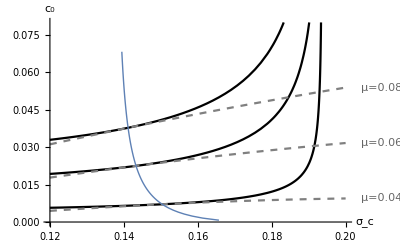

```mathematica
params1={rf->-0.015,μ->0.04,σ->0.18,γ-> 3,ρ->0.075};
params2={rf->-0.015,μ->0.06,σ->0.18,γ-> 3,ρ->0.075};
params3={rf->-0.015,μ->0.08,σ->0.18,γ-> 3,ρ->0.075};
baseparams={rf-> -0.015,σ->0.18,γ-> 3,ρ->0.075};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
μList=Range[0.01,0.12,0.001];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{μ->μsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{μ->μsub},{σc,v},Reals][[1]]/.baseparams/.{μ->μsub}},{μsub,μList}];
p1=Plot[{c01/.params1/.{v->(v/.sol1)},c02/.params1,
	c01/.params2/.{v->(v/.sol2)},c02/.params2,
	c01/.params3/.{v->(v/.sol3)},c02/.params3},
{σc,0.12,0.20},PlotRange->{0.0,0.08},PlotStyle->{Black,{Dashed,Gray}},
PlotLabels->{None,"μ=0.04",None,"μ=0.06",None,"μ=0.08"},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->Thick,Joined->True];
Show[p1,p2]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

Consumption for different values of r_f for γ<1

```mathematica
params1={rf->-0.025,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
params2={rf->0.0,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
params3={rf->0.025,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
baseparams={μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075,Infl->0};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
vsol1=v/.sol1;
vsol2=v/.sol2;
vsol3=v/.sol3;
rfList=Range[-0.03,0.5,0.002];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]]/.baseparams},{rfsub,rfList}];
p1=Plot[{c01/.params1/.{v->vsol1},c02/.params1/.{v->vsol1},
	c01/.params2/.{v->vsol2},c02/.params2/.{v->vsol2},
	c01/.params3/.{v->vsol3},c02/.params3/.{v->vsol3}},
{σc,0.2,(√((2ρ)/(γ-1)^2))/.baseparams},PlotRange->{-0.01,0.1},PlotStyle->{Black,{Dashed,Gray}},
PlotLabels->Placed[{"","r_f=-0.025","","r_f=0.0","","r_f=0.025"},Below],
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->Thick, Joined->True,PlotStyle->PointSize[0.05]];
figure2=Show[p1,p2]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/graph_analysis_vary_rf_gamma_less_than_1.pdf",figure2,"PDF"]
```

### Share of Wealth Given Up to Have the Same Value as a Constrained Investor

#### Arithmetic Model

```mathematica
StandardModelParams={μc->(rf-ρ)/γ+γ/(2 γ^2)(μ/σ)^2,σc-> μ/(γ σ),cw->ρ/γ+(γ-1)/γ(rf+1/(2γ)(μ/σ)^2)};
αAr=(-rf+√(rf^2+2ρ ((1+γ)/γ)(μ/σ)^2))/(μ(1+γ));
ArModelParams={σcAr->αAr σ,cwAr->rf+αAr μ};
η=If[ρ-γ(γ-1)(σcAr)^2/2>0,-(1-((ρ-γ(γ-1)(σcAr)^2/2)^(1/(γ-1)))/((ρ+(γ-1)μc-(γ-1)^2 σc^2/2)^(1/(γ-1)))*cwAr/cw),Missing]/.StandardModelParams/.ArModelParams;
lossSustArPlot=Plot[{η/.{μ->0.06}/.{γ->3,ρ->0.075,σ->0.18}},{rf,-0.15,0.07},PlotRange->{{-0.06,0.07},{-1,0}},AxesLabel->{"r_f","Wealth-Equivalent Utility Loss"},BaseStyle->{FontSize->12}];
```

#### Geometric Model

```mathematica
Clear[f,μ,σ];
f=(rf+α μ-1/2 α^2 σ^2)/(1-γ)-1/2 α(μ-α σ^2)+(ρ(μ-α σ^2))/((1-γ)^2 α σ^2);
rfList=Range[-0.2,0.09,0.0005];
Consumption=rf+α μ-1/2 α^2 σ^2;
toSolve={f==0&&α>0&&Consumption>0&&μ-α σ^2>0};
A=-(rf+α μ-1/2 α^2 σ^2)^-γ(μ-α σ^2)/((1-γ)α σ^2);
rfCompStat=-γ(rf+α μ-1/2 α^2 σ^2)^(-γ-1)(μ-α σ^2)+(1-γ)D[A,rf]α σ^2;
RepList1=Table[Join[{rf->rfSub},First[Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.05,σ->0.18,rf->rfSub},α,Reals]],{α->Missing}]],{rfSub,rfList}];
RepList2=Table[Join[{rf->rfSub},First[Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.06,σ->0.18,rf->rfSub},α,Reals]],{α->Missing}]],{rfSub,rfList}];
RepList3=Table[Join[{rf->rfSub},First[Evaluate[NSolve[toSolve/.{γ->3,ρ->0.075,μ->0.07,σ->0.18,rf->rfSub},α,Reals]],{α->Missing}]],{rfSub,rfList}];
```

```mathematica
StandardModelParams={μc->(rf-ρ)/γ+γ/(2 γ^2)(μ/σ)^2,σc-> μ/(γ σ),cw->ρ/γ+(γ-1)/γ(rf+1/(2γ)(μ/σ)^2)};
GeometricModelParams={σcGeom->α σ,cwGeom->rf+α μ-1/2 α^2 σ^2};
η=(1-((ρ-(γ-1)^2(σcGeom)^2/2)^(1/(γ-1)))/((ρ+(γ-1)μc-(γ-1)^2 σc^2/2)^(1/(γ-1)))*cwGeom/cw);
ηList1={rf,-η}/.StandardModelParams/.GeometricModelParams/.{γ->3,ρ->0.075,μ->0.05,σ->0.18}/.RepList1;
ηList2={rf,-η}/.StandardModelParams/.GeometricModelParams/.{γ->3,ρ->0.075,μ->0.06,σ->0.18}/.RepList2;ηList3={rf,-η}/.StandardModelParams/.GeometricModelParams/.{γ->3,ρ->0.075,μ->0.07,σ->0.18}/.RepList3;
lossSustGeomPlot=ListPlot[{ηList2},AxesLabel->{"r_f","Wealth-Equivalent Utility Loss"},
Joined->True,BaseStyle->{FontSize->12},PlotRange->{{-0.06,0.09},{-1,0}}];
(*ListPlot[{ηList1,ηList2,ηList3},
PlotLabels->{"μ=0.05","μ=0.06","μ=0.07"},AxesLabel->{"r_f","Wealth-Equivalent Utility Loss"},
Joined->True,BaseStyle->{FontSize->12},PlotRange->{{-0.09,0.07},{-1,0}}]*)
```

#### Constrained by Merton Portfolio Allocation

```mathematica
η=If[ρ+(γ-1)μcConst-(γ-1)^2(σcConst)^2/2>0,(1-((ρ+(γ-1)μcConst-(γ-1)^2(σcConst)^2/2)^(1/(γ-1)))/((ρ+(γ-1)μc-(γ-1)^2 σc^2/2)^(1/(γ-1)))*cwConst/cw),Missing];
ArModelParams={μcConst->-1/(2 γ^2)(μ/σ)^2,σcConst->1/γ μ/σ,cwConst-> rf+1/γ(μ/σ)^2};
StandardModelParams={μc->(rf-ρ)/γ+γ/(2 γ^2)(μ/σ)^2,σc-> μ/(γ σ),cw->ρ/γ+(γ-1)/γ(rf+1/(2γ)(μ/σ)^2)};
lossMertonArPlot=Plot[-η/.ArModelParams/.StandardModelParams/.{μ->0.06}/.{γ->3,ρ->0.075,σ->0.18},{rf,-0.1,0.25},
PlotRange->{{-0.06,0.07},{-1,0}},PlotStyle->{Dashed,ColorList[[2]]},AxesLabel->{"r_f","Wealth Equivalent Utility Loss"},BaseStyle->{FontSize->12}];
GeometricModelParams={μcConst->0,σcConst->1/γ μ/σ,cwConst-> rf+1/γ(μ/σ)^2(1-1/(2γ))};
lossMertonGeomPlot=Plot[-η/.GeometricModelParams/.StandardModelParams/.{μ->0.06}/.{γ->3,ρ->0.075,σ->0.18},{rf,-0.1,0.1},
PlotRange->{{-0.06,0.09},{-1,0}},PlotStyle->{Dashed,ColorList[[2]]},AxesLabel->{"r_f","Wealth Equivalent Utility Loss"},BaseStyle->{FontSize->12}];
```

#### Combining Plots

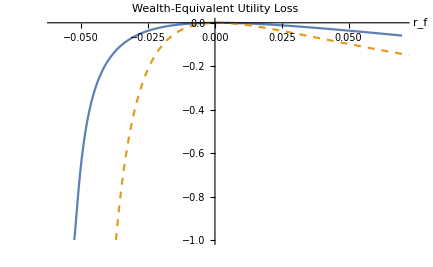

/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/comparing_losses_arithmetic.pdf

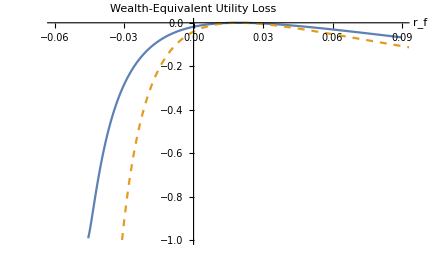

/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/comparing_losses_geometric.pdf

```mathematica
plot6=Show[lossSustArPlot,lossMertonArPlot]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/comparing_losses_arithmetic.pdf",plot6,"PDF"]
plot7=Show[lossSustGeomPlot,lossMertonGeomPlot]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/comparing_losses_geometric.pdf",plot7,"PDF"]
```

Comparing losses for the arithmetic and geometric constraints

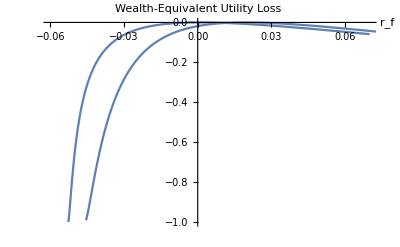

```mathematica
Show[lossSustArPlot,lossSustGeomPlot]
```

### Figures for γ < 1

```mathematica
BaseParams={μ->0.06,σ->0.18,γ->0.5,ρ->0.075};
rfList=Range[-0.1,0.10,0.001];
p1=ListPlot[{
Table[{rsub,α/.NSolve[{h==0&&α>0&&μ-α σ^2<0}/.{γ->0.5,ρ->0.075,μ->0.02,σ->0.18}/.{r->rsub},α][[1]]},{rsub,rfList}],
Table[{rsub,α/.NSolve[{h==0&&α>0&&μ-α σ^2<0}/.{γ->0.5,ρ->0.075,μ->0.06,σ->0.18}/.{r->rsub},α][[1]]},{rsub,rfList}],
Table[{rsub,α/.NSolve[{h==0&&α>0&&μ-α σ^2<0}/.{γ->0.5,ρ->0.075,μ->0.07,σ->0.18}/.{r->rsub},α][[1]]},{rsub,rfList}]},
PlotLabels->{"μ=0.05","μ=0.06","μ=0.07"},AxesLabel->{"r_f","Risky Share α"},
Joined->True,BaseStyle->{FontSize->12}
]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/opt_alpha_diff_mu_gamma_below_1.pdf",p1,"PDF"]
```

-Graphics-

/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/opt_alpha_diff_mu_gamma_below_1.pdf

```mathematica
NSolve[{μ/σ+√((μ/σ)^2+2rf)==√((2ρ)/(γ-1)^2)}/.{γ->0.5,ρ->0.075,μ->0.06,σ->0.18},rf]
-1/2(μ/σ)^2/.{γ->0.5,ρ->0.075,μ->0.06,σ->0.18}
```

{{rf→0.0418011}}

-0.0555556

```mathematica
Solve[]
```

```mathematica
(* Graphically illustrating changing the risk free rate *)
ClearAll[c01,c02,v];
c01=(ρ-(1-γ)^2 σc^2/2)^(-1/(γ-1))(1/((1-γ)v))^(1/(γ-1));
c02=rf+σc/σ μ-1/2 σc^2;
params1={rf->-0.025,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
params2={rf->0.0,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
params3={rf->0.025,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
baseparams={μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v<0}/.params3,{σc,v},Reals][[1]];
vsol1=v/.sol1;
vsol2=v/.sol2;
vsol3=v/.sol3;
rfList=Range[-0.15,0.5,0.002];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v>0};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{rf->rfsub},{σc,v},Reals][[1]]/.baseparams},{rfsub,rfList}];
p1=Plot[{c01/.params1/.{v->vsol1},c02/.params1/.{v->vsol1},
	c01/.params2/.{v->vsol2},c02/.params2/.{v->vsol2},
	c01/.params3/.{v->vsol3},c02/.params3/.{v->vsol3}},
{σc,0.3,0.8},PlotStyle->{Black,{Dashed,Gray}},
PlotLabels->{None,"r_f=-0.025",None,"r_f=0.0",None,"r_f=0.025"},
PlotRange->{-0.02,0.1},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->Thick, Joined->True,PlotStyle->PointSize[0.05]];
figure2=Show[p1,p2]
Export["/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/graph_analysis_vary_rf_gamma_below_1.pdf",figure2,"PDF"]
```

-Graphics-

/Users/rsigalov/Dropbox/Reaching for Yield/Write-up/figures/graph_analysis_vary_rf_gamma_below_1.pdf

```mathematica
(* Graphically illustrating changing the discount rate *)
params1={rf->0.02,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.07};
params2={rf->0.02,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.075};
params3={rf->0.02,μ->0.06,σ->0.18,γ-> 0.5,ρ->0.10};
sol1=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v>0}/.params1,{σc,v},Reals][[1]];
sol2=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v>0}/.params2,{σc,v},Reals][[1]];
sol3=NSolve[{c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v>0}/.params3,{σc,v},Reals][[1]];
ρList=Range[0.01,0.2,0.005];
toSolveMech={c01==c02 &&D[c01,σc]==D[c02,σc]&&σc>0&&v>0};
baseparams={μ->0.06,σ->0.18,γ-> 0.5,rf->0.02};
optPoints=Table[{
σc/.NSolve[toSolveMech/.baseparams/.{ρ->ρsub},{σc,v},Reals][[1]],
c01/.NSolve[toSolveMech/.baseparams/.{ρ->ρsub},{σc,v},Reals][[1]]/.baseparams/.{ρ->ρsub}},{ρsub,{0.07,0.075,0.10}}];
p1=Plot[{c01/.params1/.sol1,c02/.params1/.sol1,
	c01/.params2/.sol2,c02/.params2/.sol2,
	c01/.params3/.sol3,c02/.params3/.sol3},
{σc,0.05,0.8},PlotRange->{0.0,0.10},PlotStyle->{Black,{Dashed,Gray}},
AxesLabel->{"σ_c","c_0"}, BaseStyle->{FontSize->12}];
p2=ListPlot[optPoints,PlotStyle->PointSize[0.02]];
Show[p1,p2]
```

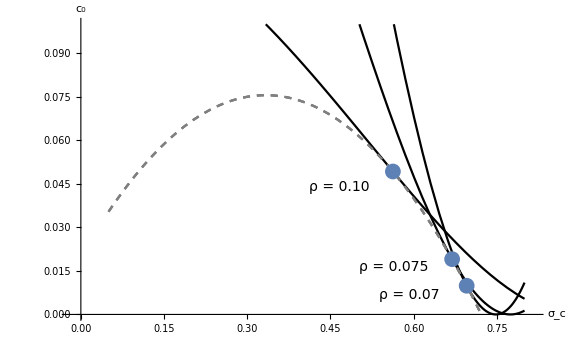

### General Equilibrium

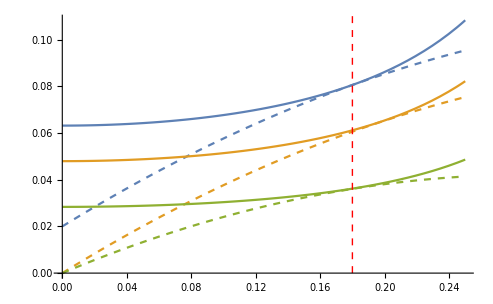

```mathematica
(* Plotting transition in risk premium in response to a change in the risk free rate *)
c01=(ρ-(1-γ)^2 σc^2/2)^(-1/(γ-1))(1/((1-γ)v))^(1/(γ-1));
c02=rf+σc/σ μ-1/2 σc^2;
baseparams ={γ->2, ρ->0.075, σ->0.18};
ColorList=ColorData[97,"ColorList"];
lineStyle={Thick,Red,Dashed};
line1=Line[{{σ/.baseparams,0},{σ/.baseparams,0.5}}];
Plot[
{c01/.baseparams/.{v->-211},
c02/.baseparams/.{μ->0.0768,rf->0.02},
c01/.baseparams/.{v->-278},
c02/.baseparams/.{μ->0.0768,rf->0.0},
c01/.baseparams/.{v->-470},
c02/.baseparams/.{μ->0.0523,rf->0.0}},{σc,0,0.25},
PlotStyle->{
ColorList[[1]], {Dashed,ColorList[[1]]},
ColorList[[2]], {Dashed,ColorList[[2]]},
ColorList[[3]], {Dashed,ColorList[[3]]}},
Epilog->{Directive[lineStyle],line1}]
```